```mathematica
Begin["BoatContext`"];
libboatLocation="libboat.nb";
libboat=NotebookOpen[libboatLocation];
SelectionMove[libboat,All,Notebook];
SelectionEvaluate[libboat];
Needs["CUDALink`"];
```

```mathematica
bHullFileLocation="bhull.stl";
hullFileLocation="hull.stl";

bHullFileLocation="hulls/boats/experimentallemon.stl";
hullFileLocation="hulls/boats/experimentallemon.stl";
(*hullFileLocation="tmp.stl"*)

canFileLocation="can.stl";
can=Import[canFileLocation,"BoundaryMeshRegion"];

mastFileLocation="mast.stl";
mast=Import[mastFileLocation,"BoundaryMeshRegion"];

(* Convert from STL file units to cm *)
stlUnits="Meters";
stlScale=QuantityMagnitude[UnitConvert[stlUnits,Quantity[, "Centimeters"]]];

(* Generate point cloud *)
buoyHullNonScaled=Import[bHullFileLocation,"BoundaryMeshRegion"];
buoyHull=TransformedRegion[buoyHullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*buoyHull=Import["hulls/cube/cube.stl","BoundaryMeshRegion"];*)
buoyHullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
buoyHullPoints=pointCloud[buoyHull,100000];
buoyHullCentroid=RegionCentroid[buoyHull];

hullNonScaled=Import[hullFileLocation,"BoundaryMeshRegion"];
hull=TransformedRegion[hullNonScaled,ScalingTransform[{stlScale,stlScale,stlScale}]];
(*hull=Import["hulls/cube/cube.stl","BoundaryMeshRegion"];*)
hullVolume=Volume[buoyHull]Quantity[, ("Centimeters")^3];
hullCentroid=RegionCentroid[hull];

(* Constants *)
(*GeogravityModelData[CityData[Entity["City",{"Needham","Massachusetts","UnitedStates"}],"Coordinates"],"Magnitude"];*)
g=9.81 Quantity[, ("Meters")/("Seconds")^2];
blueFoamDensity=0.0317 Quantity[, ("Grams")/("Centimeters")^3];
waterDensity=1 Quantity[, ("Grams")/("Centimeters")^3];
```

```mathematica
"tmp.stl"
```

```mathematica
can1Loc={0,4.5-2,9.35};
can2Loc={0,4.5-2,26};

canLocs=canLocationFinder[buoyHullCentroid,8,-3.6];
can1Loc=canLocs[[1]];
can2Loc=canLocs[[2]];

mastLoc=mastLocationFinder[buoyHullCentroid,25-8.5];

ballast1=ballastLocationFinder[buoyHullCentroid,-12];
ballast2=ballastLocationFinder[buoyHullCentroid,-9];
ballast3=ballastLocationFinder[buoyHullCentroid,-9];

frontVec=Normalize[{1,0,0}];
boat={
<|
name->"BuoyHull",
type->"Buoy",
mass->buoyHullVolume*waterDensity,
volume->buoyHullVolume,
points->buoyHullPoints,
region->buoyHull,
render->{GraphicsComplex[MeshCoordinates@buoyHull,MeshCells[buoyHull,2]]},
cobRender->({White,PointSize[Large],Point[#]}&)
|>,
<|
name->"Hull",
type->"PointMass",
mass->hullVolume*blueFoamDensity,
volume->hullVolume,
com->Quantity[hullCentroid,"Centimeters"],
render->{
{Black,PointSize[Large],Point[hullCentroid]},
{EdgeForm[],Opacity[.6],LightPink,GraphicsComplex[MeshCoordinates@hull,MeshCells[hull,2]]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can1Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can1Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can1Loc]}
}
|>,
<|
name->"Can",
type->"PointMass",
mass->389.5 Quantity[, "Grams"],
com->Quantity[can2Loc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[can2Loc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@can,MeshCells[can,2]],can2Loc]}
}
|>,
<|
name->"Mast",
type->"PointMass",
mass->96.2 Quantity[, "Grams"],
com->Quantity[mastLoc,"Centimeters"],
render->{
{Black,PointSize[Large],Point[mastLoc]},
{EdgeForm[],Opacity[.6],LightGray,Translate[GraphicsComplex[MeshCoordinates@mast,MeshCells[mast,2]],mastLoc]}
}
|>(*,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast1,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast2,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>,
<|
name->"Ballast",
type->"PointMass",
mass->100Quantity[, "Grams"],
com->Quantity[ballast3,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>*)
};
regionBounds[boat]

Grid[Transpose@{Table[stressTest[buoyHullPoints,x],{x,Range[30]}]}]
```

{{0.,60.},{-10.77,10.77},{0.0600001,17.25}}

cuda | 0.013326
cudacached | 0.000134
cuda | 0.02165
cudacached | 0.000232
cuda | 0.031569
cudacached | 0.000317
cuda | 0.041874
cudacached | 0.000655
cuda | 0.052062
cudacached | 0.000736
cuda | 0.061944
cudacached | 0.000548
cuda | 0.075152
cudacached | 0.000625
cuda | 0.086427
cudacached | 0.000734
cuda | 0.0942
cudacached | 0.001037
cuda | 0.104058
cudacached | 0.00088
cuda | 0.115991
cudacached | 0.00106
cuda | 0.131674
cudacached | 0.001118
cuda | 0.138476
cudacached | 0.001176
cuda | 0.147819
cudacached | 0.001489
cuda | 0.155535
cudacached | 0.001288
cuda | 0.171212
cudacached | 0.001454
cuda | 0.180203
cudacached | 0.001739
cuda | 0.192178
cudacached | 0.00171
cuda | 0.200715
cudacached | 0.001888
cuda | 0.208767
cudacached | 0.001947
cuda | 0.219671
cudacached | 0.001844
cuda | 0.229792
cudacached | 0.001946
cuda | 0.279866
cudacached | 0.002345
cuda | 0.305951
cudacached | 0.002293
cuda | 0.325692
cudacached | 0.002417
cuda | 0.336484
cudacached | 0.002491
cuda | 0.343171
cudacached | 0.001305
cuda | 0.366079
cudacached | 0.001188
cuda | 0.381628
cudacached | 0.00107
cuda | 0.391539
cudacached | 0.001389

```mathematica
calculateAVS[boat,30,{-Pi,Pi}]
```

InterpolatingFunction[{{-3.14159, 3.14159}}, <>]

```mathematica
sortPoints[Take[buoyHullPoints,5],N[Normalize[{1,0,1}]]]
```

{16.4753,20.4756,30.8249,35.155,35.6286}

```mathematica
waterLine[boat,Normalize[{1,0,1}], buoyHullVolume/4]
```

21.5038

```mathematica
GraphicsGrid[{{Show[renderBoatWithForces[boat,Normalize[{0,0,1}]],ViewPoint->{0,-∞,0}],
Show[renderBoatWithForces[boat,Normalize[{0,0,1}]],ViewPoint->{∞,0,0}]},{
Show[renderBoatWithForces[boat,Normalize[{0,0,1}]],ViewPoint->{0,0,∞}]}},ImageSize->Full]
exportBoat[boat,"boat.json"]
```

-Graphics-

boat.json

```mathematica
"boat.json"
```

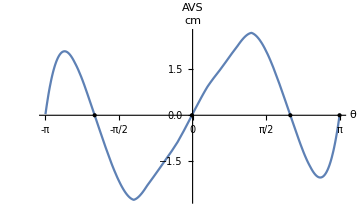
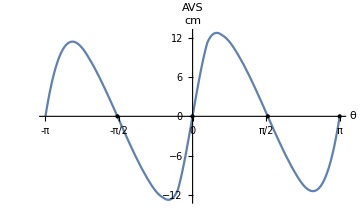
Boat | -Graphics3D-
AVS Plot | -Graphics-
AVS Zeros | -119.819 ° | -0.824277 ° | 119.572 ° | 179.808 °
Trim AVS | -Graphics-
Trim | -0.0840243 °

```mathematica
boatSummary[boat]//RuntimeTools`Profile
```

```mathematica
exportBoat[boat,"boat.json"]
```

```mathematica
"boat.json"
```

```mathematica
<|
name->"Ballast",
type->"PointMass",
mass->100 Quantity[, "Grams"],
com->Quantity[ballast1,"Centimeters"],
render->{
{Black,PointSize[Large],Point[ballast1]}
}
|>
```

```mathematica
"boat.json"
```

## Boats

```mathematica
renderBoat[boat,Normalize[{0,0,1}]]
```

-Graphics3D-

```mathematica
manyBoats[boat,10,FrontVec->{1,0,0},ViewPoint->{∞,0,0}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

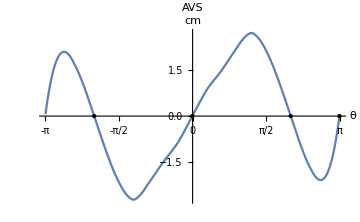
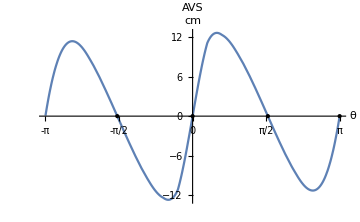
Boat | -Graphics3D-
AVS Plot | -Graphics-
AVS Zeros | -120.382 ° | -0.305391 ° | 120.088 ° | 179.694 °
Trim AVS | -Graphics-
Trim | 0.0150068 °

```mathematica
boatSummary[boat]
```

```mathematica
Links[]
LinkActivate[Links[][[4]]]
```

{LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…],LinkObject[…]}

LinkObject[…]

```mathematica
LinkReadyQ[LinkObject[…]]
```

False

```mathematica
LinkReadyQ[LinkObject[…]]
```

False

```mathematica
ParallelNeeds["CUDALink`"];
Needs["CUDALink`"];
CUDAQ[]
```

False